```mathematica
f[x_]:=1-ⅇ^(-1/4(x))
g[x_]:=4Log[1/(1-x)]
```

```mathematica
n=3 10^6;
l=100 n;
s =0;
For[i=0,i<n,i++,
For[j=0,j+=N[g[RandomReal[]]]<1,s+=300,0]
]
```

```mathematica
s/3
```

66468300

```mathematica
66359765-----;
66346800
66578400
85207600----;
85660800
100000000
```

```mathematica
N[f[1]]*300000000
```

6.63598×10^7

```mathematica
NumberForm[6.635976507857854*^7,16]
```

6.635976507857853×10^7

```mathematica
Sum[(1-1/ⅇ^(1/4))^i,{i,1,∞}]
```

```mathematica
N[-1+ⅇ^(1/4)]
```

```mathematica
0.2840254166877414*3
```

0.852076

```mathematica
f[1]
```

```mathematica
N[1-1/ⅇ^(1/4)]
```

0.221199

```mathematica
N[4-5*(1-f[1])]
```

0.105996

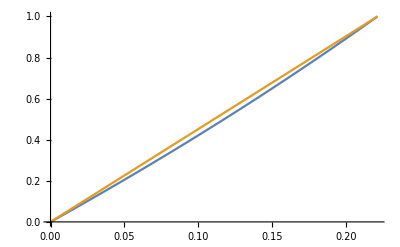

```mathematica
Plot[{g[x],x/f[1]},{x,0,f[1]}]
```

```mathematica
f[x_]:=-x ⅇ^(-x/4)-4 ⅇ^(-x/4);g[x_]:=1-ⅇ^(-x/4);
```

```mathematica
a=1;b=1;c=b;
```

```mathematica
b *= g[a];
c=Expand[c+b]
a=a-(f[a]-f[0]);
```

2-1/ⅇ^(1/4)+(1-1/ⅇ^(1/4)) (1-ⅇ^(3/4-5/(4 ⅇ^(1/4))))

```mathematica
a=1;b=1;
s=Sum[b*=g[a];a=N[a-(f[a]-f[0])];b,{i,1,10}]
```

0.275213

```mathematica
300 s
```

82.564

```mathematica
a=1;b=1;c=0;s=Table[b*=g[a];a=N[a-(f[a]-f[0])];c+=b,{i,1,20}];
```

```mathematica
s
```

{1-1/ⅇ^(1/4),0.265502,0.273604,0.274966,0.275178,0.275209,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213,0.275213}

```mathematica
N[g[1]]*3
```

0.663598

```mathematica
0.275213*3000000
```

825639.

```mathematica
a=1;b=1;c=0;
```

```mathematica
b*=g[a];a=N[a-(f[a]-f[0])];c+=N[b]
```

0.221199

```mathematica
g[a]*b
```

0.0443031

```mathematica
66359765-----;
66346800
66578400
```

```mathematica
66578400/3
```

22192800

```mathematica
N[1-1/ⅇ^(1/4)]
```

```mathematica
0.221199
0.221928
```